# Battle Plan

This document describes the actions we should take in case of a market crash.

### Identifying a Crash

The first thing to do is to determine if a crash is even happening. The heuristic we use here is to know how much the market has crashed in terms of standard deviations.

Any drop below 2 standard deviations is no evidence of a crash. A drop of 3 standard deviations is called a 3-σ crash, a drop of 4 standard deviations is called a 4-σ crash, etc.

```mathematica
ts=FinancialData[
"NASDAQ:QQQ",
"Return",
{
CurrentDate[]-Quantity[20,"Years"],
CurrentDate[]
}
]//TimeSeriesMap[#+1&,#]&;
```

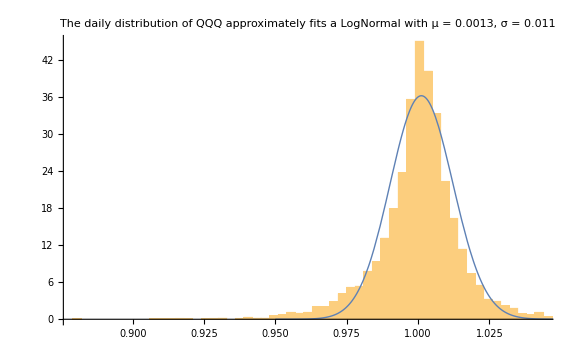

```mathematica
mean:=0.0013
stDev:=0.011
dist:=LogNormalDistribution[mean,stDev]

pdf:=PDF[dist]

Show[
Histogram[ts,{0.003}, "PDF", ImageSize->Large, PlotLabel->"The daily distribution of QQQ approximately fits \na LogNormal with μ = "<>ToString[mean] <>", σ = " <> ToString[stDev]],
Plot[pdf[x],{x,0.95,1.05}, PlotStyle->Thick, ImageSize->Large]
]
```

This gives us a very practical approximation for identifying crashes: since a 1% drop of QQQ is a 1-σ move, then a 3% drop is a 3-σ move.

### How often should we expect n-σ moves in the market

By looking at the empirical probabilities, we can get an idea of how often large moves occur in the market. Although there is no guarantee that the future will look like the past, its good to have an idea of these probabilities.

```mathematica
EmpiricalProbabilityOfSigmaMove[nSigma_]:=With[{values=Values[ts]},
N[
Count[values,#<Exp[mean-nSigma*stDev]& ]/Length[values]
]
];

Grid[{
{"n-σ", "Empirically, how often does it happen? (in days)", "Or approximately..."},
{2,1/EmpiricalProbabilityOfSigmaMove[2], "once every two weeks"},
{3,1/EmpiricalProbabilityOfSigmaMove[3], "once per month"},
{4,1/EmpiricalProbabilityOfSigmaMove[4], "once every two months"},
{5,1/EmpiricalProbabilityOfSigmaMove[5], "once every half a year"},
{6,1/EmpiricalProbabilityOfSigmaMove[6], "once every year"},
{7,1/EmpiricalProbabilityOfSigmaMove[7], "once every 2 years"}
},
 Frame->All
]
```

n-σ | Empirically, how often does it happen? (in days) | Or approximately...
2 | ComplexInfinity | once every two weeks
3 | ComplexInfinity | once per month
4 | ComplexInfinity | once every two months
5 | ComplexInfinity | once every half a year
6 | ComplexInfinity | once every year
7 | ComplexInfinity | once every 2 years